# pFDA Trial Results

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\nathanm\OneDrive\dinosaur research\fabbri et al rebuttal\mathematica for github

```mathematica
log10ticks = Join[Table[{k,10^k},{k,0,3}],Flatten[Table[{Log[10,j*10^k],""},{k,0,3},{j,2,9,1}],1]];
```

```mathematica
mswordsize = 6.5*72;
```

```mathematica
cvnamerules = Table[StringJoin["D",ToString[i],"_analysis"]-> {StringJoin["D",ToString[i]],If[EvenQ[i],"Rib","Femur"]},{i,1,14}]
```

{D1_analysis→{D1,Femur},D2_analysis→{D2,Rib},D3_analysis→{D3,Femur},D4_analysis→{D4,Rib},D5_analysis→{D5,Femur},D6_analysis→{D6,Rib},D7_analysis→{D7,Femur},D8_analysis→{D8,Rib},D9_analysis→{D9,Femur},D10_analysis→{D10,Rib},D11_analysis→{D11,Femur},D12_analysis→{D12,Rib},D13_analysis→{D13,Femur},D14_analysis→{D14,Rib}}

## Fabbri et al Data

### Overall data and name matching

```mathematica
femurspellcorrection = {"Spheniscus"-> "Spheniscus_humboldti","Noemys_fodies"-> "Neomys_fodiens","Anas_erythroincha" -> "Anas_erythrorhyncha","Pelecanoides_urinatryx"->"Pelecanoides_urinatrix","Phaeton_aethereus"->"Phaethon_aethereus","Rynochetus_jubatus"-> "Rhynochetos_jubatus", "Sula"-> "Sula_dactylatra","Tachybaptus"-> "Tachybaptus_ruficollis","Trybonix_ventralis"-> "Tribonyx_ventralis","Turdus_olivator"-> "Turdus_olivater","Uria"-> "Uria_sp","Chapsosaurus"-> "Champsosaurus","Ichtyosaur_sp"-> "Ichthyosaur_sp","Ichtyosaurus"-> "Ichthyosaurus"};
```

```mathematica
ribspellcorrection = {"Aramus_guarana"-> "Aramus_guarauna","Charcarodontosaurid"->"Carcharodontosaurid","Chaunia_chavaria"-> "Chauna_chavaria","Glareola_pratincula"->"Glareola_pratincola","Tachyeres_ciconia"-> "Tachyeres_sp", "Pelecanoides_urinatryx"->"Pelecanoides_urinatrix","Phaeton_aethereus"->"Phaethon_aethereus","Tachybaptus_ruficolus"-> "Tachybaptus_ruficollis","Rhinocerus_unicornis"->"Rhinoceros_unicornis","Phaenicopterus_roseus"-> "Phoenicopterus_roseus","Phalacrocorax_harris"->  "Phalacrocorax_harrisi","Noemys_fodies"->"Neomys_fodiens"};
```

```mathematica
allspellcorrection = Union[Join[femurspellcorrection,ribspellcorrection]];
```

```mathematica
DuplicateFreeQ[allspellcorrection[[All,1]]]
```

True

```mathematica
femurrawraw= Import["2021-07-11463C-Bone density dataset.csv"];
fabbriallfemurraw  =( Drop[Drop[femurrawraw,1],-1]/.s_String :> StringTrim[StringTrim[s,"_"..],"."..])/.femurspellcorrection;
```

```mathematica
ribrawraw = Import["2021-07-11463C-Bone density dataset - ribs.csv"];
fabbriallribraw = ( Drop[ribrawraw,1]/.s_String :> StringTrim[StringTrim[s,"_"..],"."..])/.ribspellcorrection;
```

```mathematica
femurrawraw[[1]] == ribrawraw[[1]]
```

False

```mathematica
fpointrule = Map[#[[1]]-> Drop[#,1]&,fabbriallfemurraw[[All,{1,12,13,11,9}]]];
```

```mathematica
rpointrule = Map[#[[1]]-> Drop[#,1]&,fabbriallribraw[[All,{1,12,13,11,9}]]];
```

```mathematica
originalclassrule = Map[#[[1]]-> Drop[#,1]&,Union[fabbriallfemurraw[[All,{1,12,13}]],fabbriallribraw[[All,{1,12,13}]]]];
```

```mathematica
{Range[Length[femurrawraw[[1]]]],femurrawraw[[1]],ribrawraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15 | 16 | 17 | 18
taxa | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD log | Flying | Diving | finest.category | diving.or.not | Morphsource specimen identifier | Morphosource specimen link | Morphosource scan link
Taxon | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD Log | Flying | Diving | finest.category | diving.or.not | Morphsource specimen identifier | Morphosource specimen link | Morphosource scan link

```mathematica
femurnonflyingrule =Map[#-> 1&,Cases[fabbriallfemurraw[[All,{1,12,13}]],{_,0,0|2}][[All,1]]];
ribnonflyingrule =Map[#-> 1&,Cases[fabbriallribraw[[All,{1,12,13}]],{_,0,0|2}][[All,1]]];
nonflyingrule = Union[femurnonflyingrule,ribnonflyingrule];
```

```mathematica
fabbriallfemurnames =fabbriallfemurraw[[All,1]];
```

```mathematica
fabbriallribnames =fabbriallribraw[[All,1]];
```

```mathematica
fcallrawraw =Import["femur compactness all.csv"];
fcallraw =Sort[ Drop[(fcallrawraw/.s_String :> StringTrim[StringTrim[s,"_"..],"."..])/.femurspellcorrection,1]];
```

```mathematica
femurincodenotlist = Complement[fcallraw[[All,1]],fabbriallfemurnames]
```

{Phoenicopterus_roseus}

```mathematica
femurinlistnotcode = Complement[fabbriallfemurnames,fcallraw[[All,1]]]
```

{Phoenicopterus_ruber}

```mathematica
fcrawraw = Import["femur compactness all no graviportals and pelagic.csv"];fcraw= Sort[(Drop[fcrawraw,1]/.s_String :> StringTrim[StringTrim[s,"_"..],"."..])/.femurspellcorrection];
```

```mathematica
Complement[fcraw[[All,1]],fcallraw[[All,1]]]
```

{}

```mathematica
riballcrawraw = Import["ribs compactness all.csv"];
riballcraw=Sort[(Drop[riballcrawraw,1]/.s_String :> StringTrim[StringTrim[s,"_"..],"."..])/.ribspellcorrection];
```

```mathematica
Count[riballcraw[[All,{12,13}]],{0,0}]
```

63

```mathematica
Count[riballcraw[[All,{12,13}]],{0,2}]
```

49

```mathematica
ribincodenotlist = Complement[riballcraw[[All,1]],fabbriallribnames]
```

{}

```mathematica
Complement[fabbriallribnames,riballcraw[[All,1]]]
```

{}

```mathematica
ribcrawraw = Import["ribs compactness all no graviportals no pelagic.csv"];ribcraw= Sort[Drop[(ribcrawraw/.ribspellcorrection)/.s_String :> StringTrim[StringTrim[s,"_"..],"."..],1]];
```

```mathematica
Complement[ribcraw[[All,1]],riballcraw[[All,1]]]
```

{}

#### Check coordinates

```mathematica
{Range[Length[fcallrawraw[[1]]]],fcallrawraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
taxa | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD log | Flying | Diving | finest.category | diving.or.not

```mathematica
{Range[Length[riballcrawraw[[1]]]],riballcrawraw[[1]]}//TableForm
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13 | 14 | 15
Taxon | Reference | Specimen | Type of data | AFA | ALA | FAD | LAD | Global compactness | MD (mm) | MD Log | Flying | Diving | finest.category | diving.or.not

```mathematica
fcallcodepoints = Map[{#[[1]],{#[[11]],#[[9]]},"code"}&,fcallraw];
```

```mathematica
ribcallcodepoints = Map[{#[[1]],{#[[11]],#[[9]]},"code"}&,riballcraw];
```

```mathematica
fabbriallfemurpoints =  Map[{#[[1]],{#[[11]],#[[9]]},"list"}&,fabbriallfemurraw];
```

```mathematica
fabbriallribpoints =  Map[{#[[1]],{#[[11]],#[[9]]},"list"}&,fabbriallribraw];
```

```mathematica
femurcodelisttogether = GatherBy[Join[fcallcodepoints,fabbriallfemurpoints],First];
```

```mathematica
Cases[femurcodelisttogether,a_List/;Length[a]!=2]
```

{{{Champsosaurus,{1.09304,0.952},code},{Champsosaurus,{0.89487,0.968},code},{Champsosaurus,{0.89487,0.968},list},{Champsosaurus,{1.09304,0.952},list}},{{Phoenicopterus_roseus,{1.04021,0.279},code}},{{Phoenicopterus_ruber,{1.04021,0.279},list}}}

```mathematica
Cases[femurcodelisttogether,{{name_,pt1_,where1_},{name_,pt2_,where2_}}/;pt1 != pt2]
```

{}

```mathematica
ribcodelisttogether = GatherBy[Join[ribcallcodepoints,fabbriallribpoints],First];
```

```mathematica
Cases[ribcodelisttogether,a_List/;Length[a]!=2]
```

{}

```mathematica
Cases[ribcodelisttogether,{{name_,pt1_,where1_},{name_,pt2_,where2_}}/;pt1 != pt2]
```

{}

#### Check categorical variables

```mathematica
fcallraw[[All,12]]
```

{0,2,0,0,0,0,0,2,0,2,2,2,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,2,0,UNKNOWN,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,2,0,0,1,2,0,2,0,0,2,0,0,0,0,0,0,0,0,0,0,UNKNOWN,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,UNKNOWN,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,2,2,2,0,0,2,0,0,0,0,0,2,0,0,0,2,2,0,0,0,0,2,2,UNKNOWN,2,0,0,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,1,0,0,2,0,2,0,0,0,0,2,0,UNKNOWN,0,0,1}

```mathematica
fcallraw[[All,13]]
```

{UNKNOWN,2,0,2,UNKNOWN,2,1,1,1,2,1,1,UNKNOWN,2,0,0,1,UNKNOWN,UNKNOWN,0,UNKNOWN,UNKNOWN,UNKNOWN,2,0,0,0,2,2,0,0,2,0,0,2,2,0,2,2,2,0,UNKNOWN,0,2,2,0,1,0,0,UNKNOWN,2,2,0,0,0,2,UNKNOWN,0,0,0,0,UNKNOWN,0,2,0,UNKNOWN,UNKNOWN,0,2,0,0,UNKNOWN,UNKNOWN,0,UNKNOWN,0,2,2,2,2,UNKNOWN,2,2,2,UNKNOWN,0,0,2,UNKNOWN,2,0,2,2,0,UNKNOWN,0,UNKNOWN,0,0,2,0,2,UNKNOWN,0,0,UNKNOWN,0,0,2,2,0,2,UNKNOWN,2,2,2,2,2,2,0,0,2,2,UNKNOWN,UNKNOWN,2,0,2,2,1,2,1,2,2,2,1,2,2,2,UNKNOWN,2,1,0,UNKNOWN,0,1,1,0,0,2,2,0,0,UNKNOWN,0,0,0,UNKNOWN,0,2,2,0,0,0,0,0,2,0,0,UNKNOWN,2,2,2,2,2,0,UNKNOWN,UNKNOWN,0,UNKNOWN,2,0,0,UNKNOWN,2,0,2,0,UNKNOWN,0,0,UNKNOWN,0,0,UNKNOWN,0,UNKNOWN,UNKNOWN,UNKNOWN,0,2,1,UNKNOWN,0,0,0}

```mathematica
fcraw[[All,12]]
```

{2,0,0,0,0,0,2,0,2,2,2,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,2,2,0,UNKNOWN,0,0,1,1,0,0,0,0,0,0,0,0,0,2,0,0,0,2,2,0,0,1,2,0,2,0,0,2,0,0,0,0,0,0,0,UNKNOWN,0,0,0,0,0,0,0,0,0,1,0,0,0,UNKNOWN,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,2,2,2,0,0,2,0,0,0,0,0,2,0,0,0,2,2,0,0,0,0,2,2,UNKNOWN,2,0,0,0,0,0,0,0,1,0,0,0,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,2,0,0,0,0,0,1,0,0,2,0,2,0,0,0,0,2,0,UNKNOWN,0,0,1}

```mathematica
fcraw[[All,13]]
```

{2,0,2,UNKNOWN,2,1,1,1,2,1,1,2,0,0,1,UNKNOWN,UNKNOWN,0,UNKNOWN,UNKNOWN,UNKNOWN,2,0,0,2,0,0,2,0,2,2,0,2,2,0,UNKNOWN,0,2,2,0,1,0,0,UNKNOWN,2,0,0,2,UNKNOWN,0,0,0,UNKNOWN,0,2,0,UNKNOWN,UNKNOWN,0,2,0,0,UNKNOWN,UNKNOWN,0,UNKNOWN,0,2,2,2,UNKNOWN,2,UNKNOWN,0,0,2,UNKNOWN,2,2,UNKNOWN,0,UNKNOWN,0,0,0,2,UNKNOWN,0,0,UNKNOWN,0,0,2,2,0,2,UNKNOWN,2,2,2,2,2,2,0,0,2,2,UNKNOWN,UNKNOWN,2,0,2,2,1,2,1,2,2,2,1,2,2,2,UNKNOWN,2,1,0,UNKNOWN,0,1,1,0,0,2,2,0,0,UNKNOWN,0,0,0,UNKNOWN,0,2,2,0,0,0,2,0,0,UNKNOWN,2,2,2,2,2,0,UNKNOWN,0,UNKNOWN,2,0,0,UNKNOWN,2,0,2,0,UNKNOWN,0,0,UNKNOWN,0,0,UNKNOWN,0,UNKNOWN,UNKNOWN,UNKNOWN,0,2,1,UNKNOWN,0,0,0}

```mathematica
riballcraw[[All,12]]
```

{0,0,2,2,0,2,2,2,2,0,0,0,0,2,2,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,2,0,2,0,0,0,1,1,2,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,2,0,0,2,0,0,2,0,2,0,0,0,0,2,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,0,0,0,0,0,2,0,0,0,0,0,2,0,0,0,2,2,2,0,2,2,0,0,2,2,0,0,2,2,2,0,2,2,0,0,0,0,0,0,2,0,2,0,0,0,0,0,0,0,2,0,2,2,0,0,0,0,0,0,2,0,2,0,2,2,0,0,0,0,1,0}

```mathematica
riballcraw[[All,13]]
```

{0,UNKNOWN,2,1,1,1,2,1,1,UNKNOWN,0,2,0,1,1,2,2,0,2,UNKNOWN,2,2,0,0,UNKNOWN,0,2,0,0,0,0,0,UNKNOWN,2,2,0,0,0,2,0,0,2,0,2,2,0,0,2,2,0,1,0,2,0,0,2,0,2,2,0,UNKNOWN,0,2,2,0,0,2,0,0,2,0,0,1,0,2,2,0,0,0,0,0,0,0,2,2,1,0,2,UNKNOWN,2,0,0,0,0,1,2,0,UNKNOWN,2,0,2,1,0,2,0,2,2,2,0,2,2,2,2,0,0,0,2,0,1,2,1,0,1,2,2,2,1,0,2,UNKNOWN,1,1,1,0,0,0,0,0,0,0,0,2,0,UNKNOWN,0,0,2,2,UNKNOWN,UNKNOWN,0,0,2,0,2,1,0,2,2,0,0,0,0,2,0,2,2,2,1,0,0,0,0,0}

#### Compare rib and femur taxa

```mathematica
Map[DuplicateFreeQ,{fabbriallfemurnames,fabbriallribnames,fcallraw[[All,1]],riballcraw[[All,1]]}]
```

{False,True,False,True}

```mathematica
Length[Intersection[fabbriallfemurnames,fabbriallribnames]]
```

76

```mathematica
Length[Intersection[fabbriallfemurnames,fabbriallribnames]]/Total[Map[Length,{fabbriallfemurnames,fabbriallribnames}]]//N
```

0.2

```mathematica
Length[Intersection[fabbriallfemurnames,fabbriallribnames]]/Total[Map[Length,{fabbriallfemurnames}]]//N
```

0.368932

```mathematica
Length[Intersection[fabbriallfemurnames,fabbriallribnames]]/Total[Map[Length,{fabbriallribnames}]]//N
```

0.436782

```mathematica
Length[Intersection[fcallraw[[All,1]],riballcraw[[All,1]]]]
```

77

```mathematica
Complement[Intersection[fcallraw[[All,1]],riballcraw[[All,1]]],Intersection[fabbriallfemurnames,fabbriallribnames]]
```

{Phoenicopterus_roseus}

#### Graivportal and pelagic purging

```mathematica
femurpurged = Complement[fcallraw[[All,1]],fcraw[[All,1]]]
```

{Alamosaurus,Antetonitrus,Brachyodus_onoideum,Callophoca_obscura,Ceratotherium_simum,Choeropsis_liberiensis,Desmostylus_hesperus,Dicerorhinus_sumatrensis,Elephas_maximus,Hexaprotodon_garyam,Ichthyosaur_sp,Ichthyosaurus,Leptophoca_proxima,Loxodonta_africana,Mammuthus_sp,Metryorhynchus,Rhinoceros_sondaicus,Rhinoceros_unicornis,Stegosaurus_sp}

```mathematica
femurpurgeddata = Complement[fcallraw,fcraw];
```

```mathematica
ribpurged = Complement[riballcraw[[All,1]],ribcraw[[All,1]]]
```

{Alamosaurus,Apatosaurus_sp,Balaenoptera_brydei,Behemotops_katsuiei,Brachiosaurus_sp,Callophoca_obscura,Ceratotherium_simum,Clidastes_sp,Dallasaurus_turneri,Delphinapterus_leucas,Desmostylus_hesperus,Diplodocus_sp,Elephas_maximus,Lissodelphis_borealis,Mammuthus_primigenius,Metriorhynchid_indet,Miragaia_longicollum,Mollesaurus,Monodon_monoceros,Orcinus_orca,Phoca_vitulina,Platecarpus_sp,Rhinoceros_sondaicus,Rhinoceros_unicornis,Spinophorosaurus_nigerensis,Tylosaurus_sp}

```mathematica
ribpurgeddata = Complement[riballcraw,ribcraw];
```

```mathematica
tableS5list =Map[StringReplace[#," "-> "_"]&,{
{"Antetonitrus","G"},{"Callophoca obscura","DD" },{"Ichthyosaur sp","DD"},
{"Ichthyosaurus","DD"},{"Leptophoca proxima","DD"},{"Alamosaurus","G"},{"Stegosaurus sp","G"},{"Mammuthus sp","G"},{"Elephas maximus","G"},{"Loxodonta africana","G"},{"Ceratotherium simum","G" },{"Dicerorhinus sumatrensis","G"},{"Rhinoceros sondaicus","G"},{"Rhinoceros unicornis","G"},{"Brachyodus onoideum","DD"},{"Hexaprotodon garyam","G"},{"Metryorhynchus","DD"}
},{2}];
```

```mathematica
tableS6list =Map[StringTrim[StringReplace[#," "-> "_"],"."..]&,{{"Dallasaurus turneri","Deep diver"},
{"Clidastes sp.","Deep diver"},{"Tylosaurus sp.","Deep diver"},
{"Platecarpus sp.","Deep diver"},{"Metriorhynchid indet.","Deep diver"},{"Phoca vitulina","Deep diver"},
{"Balaenoptera brydei","Deep diver"},{"Elephas maximus","Graviportal"},{"Rhinoceros sondaicus","Graviportal"},{"Ceratotherium simum","Graviportal"},{"Orcinus orca","Deep diver"},{"Lissodelphis borealis","Deep diver"},{"Monodon monoceros","Deep diver"},{"Delphinapterus leucas","Deep diver"},{"Behemotops katsuiei","Deep diver"},
{"Desmostylus hesperus", "Deep diver"},{"Mollesaurus","Graviportal"},{"Alamosaurus","Graviportal"},{"Callophoca obscura","Deep diver"},
{"Spinophorosaurus nigerensis","Graviportal"},{"Apatosaurus sp.","Graviportal"},{"Diplodocus sp.","Graviportal"},{"Brachiosaurus sp.","Graviportal"},{"Miragaia longicollum","Graviportal"},{"Mammuthus primigenius","Graviportal"},{"Rhinoceros unicornis","Graviportal"}}/.{"Graviportal"-> "G","Deep diver"-> "DD"},{2}]
```

{{Dallasaurus_turneri,DD},{Clidastes_sp,DD},{Tylosaurus_sp,DD},{Platecarpus_sp,DD},{Metriorhynchid_indet,DD},{Phoca_vitulina,DD},{Balaenoptera_brydei,DD},{Elephas_maximus,G},{Rhinoceros_sondaicus,G},{Ceratotherium_simum,G},{Orcinus_orca,DD},{Lissodelphis_borealis,DD},{Monodon_monoceros,DD},{Delphinapterus_leucas,DD},{Behemotops_katsuiei,DD},{Desmostylus_hesperus,DD},{Mollesaurus,G},{Alamosaurus,G},{Callophoca_obscura,DD},{Spinophorosaurus_nigerensis,G},{Apatosaurus_sp,G},{Diplodocus_sp,G},{Brachiosaurus_sp,G},{Miragaia_longicollum,G},{Mammuthus_primigenius,G},{Rhinoceros_unicornis,G}}

```mathematica
femurpurgednotintable5 = Complement[femurpurged,tableS5list[[All,1]]]
```

{Choeropsis_liberiensis,Desmostylus_hesperus}

```mathematica
Complement[tableS5list[[All,1]],femurpurged]
```

{}

```mathematica
ribpurgednotintable5 =Complement[ribpurged,tableS6list[[All,1]],{"Mammuthus_primigenius"}]
```

{}

```mathematica
Complement[tableS6list[[All,1]],ribpurged]
```

{}

```mathematica
Intersection[ribpurged,femurpurged]
```

{Alamosaurus,Callophoca_obscura,Ceratotherium_simum,Desmostylus_hesperus,Elephas_maximus,Rhinoceros_sondaicus,Rhinoceros_unicornis}

```mathematica
Complement[ribpurged,femurpurged]
```

{Apatosaurus_sp,Balaenoptera_brydei,Behemotops_katsuiei,Brachiosaurus_sp,Clidastes_sp,Dallasaurus_turneri,Delphinapterus_leucas,Diplodocus_sp,Lissodelphis_borealis,Mammuthus_primigenius,Metriorhynchid_indet,Miragaia_longicollum,Mollesaurus,Monodon_monoceros,Orcinus_orca,Phoca_vitulina,Platecarpus_sp,Spinophorosaurus_nigerensis,Tylosaurus_sp}

```mathematica
Complement[femurpurged,ribpurged]
```

{Antetonitrus,Brachyodus_onoideum,Choeropsis_liberiensis,Dicerorhinus_sumatrensis,Hexaprotodon_garyam,Ichthyosaur_sp,Ichthyosaurus,Leptophoca_proxima,Loxodonta_africana,Mammuthus_sp,Metryorhynchus,Stegosaurus_sp}

```mathematica
Complement[tableS5list[[All,1]],tableS6list[[All,1]]]
```

{Antetonitrus,Brachyodus_onoideum,Dicerorhinus_sumatrensis,Hexaprotodon_garyam,Ichthyosaur_sp,Ichthyosaurus,Leptophoca_proxima,Loxodonta_africana,Mammuthus_sp,Metryorhynchus,Stegosaurus_sp}

```mathematica
Complement[tableS6list[[All,1]],tableS5list[[All,1]]]
```

{Apatosaurus_sp,Balaenoptera_brydei,Behemotops_katsuiei,Brachiosaurus_sp,Clidastes_sp,Dallasaurus_turneri,Delphinapterus_leucas,Desmostylus_hesperus,Diplodocus_sp,Lissodelphis_borealis,Mammuthus_primigenius,Metriorhynchid_indet,Miragaia_longicollum,Mollesaurus,Monodon_monoceros,Orcinus_orca,Phoca_vitulina,Platecarpus_sp,Spinophorosaurus_nigerensis,Tylosaurus_sp}

## Confusion functions

```mathematica
makecombinedstats[rawdata_,datasummary_]:=
Module[{sstats},
sstats = Map[{#[[1]],Min[Drop[#,1]],Max[Drop[#,1]],Mean[Drop[#,1]],StandardDeviation[Drop[#,1]]}&,Drop[rawdata,1]];
 Map[Flatten,Transpose[{Drop[datasummary,1],Map[Drop[#,1]&,sstats]}]]
];
```

```mathematica
fabbriconfusion[stats_]:=
Module[{pstats},
pstats = Pick[stats,stats[[All,1]]/.nonflyingrule,1];
{{ Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/; orig == 2 && pred == 2],Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/;orig == 2&&pred==0]},
{ Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/;orig == 0 && pred == 2],Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/; orig == 0&&pred == 0]}}
];
```

```mathematica
confusion[stats_,thresh_]:=
Module[{pstats},
pstats = Pick[stats,stats[[All,1]]/.nonflyingrule,1];{{ Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/;min >=  thresh&& orig == 2],Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/;max < thresh && orig == 2]},
{ Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/;min >=  thresh && orig == 0],Count[pstats,{nam_,orig_,pred_,count_,median_,min_,max_,mean_,sd_}/;max <  thresh && orig == 0]}}
];
```

```mathematica
makecmat[dcount_,tcount_,dmean_,tmean_]:= {{dcount-dmean,dmean},{tmean,tcount-tmean}};
```

```mathematica
cemconfusion[stats_]:=
Module[{pstats},
pstats = Pick[stats,stats[[All,1]]/.nonflyingrule,1];{{ Count[pstats,{nam_,orig_,pred_,count_,median_}/;orig == 2 && pred == 2],Count[pstats,{nam_,orig_,pred_,count_,median_}/;orig == 2&&pred==0]},
{ Count[pstats,{nam_,orig_,pred_,count_,median_}/;orig == 0 && pred == 2],Count[pstats,{nam_,orig_,pred_,count_,median_}/;orig == 0&&pred == 0]}}
];
```

```mathematica
makecf[{a_,b_,c_,d_}]:={{a,b},{c,d}};
```

```mathematica
accuracy[{{tp_,fn_},{fp_,tn_}}]:= (tp+tn)/(tp+tn+fn+fp);
tpr[{{tp_,fn_},{fp_,tn_}}]:= tp/(tp+fn);
fpr[{{tp_,fn_},{fp_,tn_}}]:= fp/(tn+fp);
tnr[{{tp_,fn_},{fp_,tn_}}]:= tn/(tn+fp);
fnr[{{tp_,fn_},{fp_,tn_}}]:= fn/(tn+fp);
balanced[{{tp_,fn_},{fp_,tn_}}]:=( tp/(tp+fn) +tn/(tn+fp))/2;
mallows[{{tp_,fn_},{fp_,tn_}}]:= Sqrt[(tp/(tp+fp))(tp/(tp+fn))];
matthews[{{tp_,fn_},{fp_,tn_}}]:= 
Module[{top,bot},
top = (tp*tn - fp*fn);
bot = Sqrt[(tp+fp)(tp+fn)(tn+fp)(tn+fn)];
If[top ==0,Return[0];,
If[bot == 0, Return[0], Return[top/bot];];
];
];
f1score[{{tp_,fn_},{fp_,tn_}}]:=(2tp)/(2tn+fp+fn);
alltests[cmat_]:={accuracy[cmat],tpr[cmat],fpr[cmat],tnr[cmat],fnr[cmat],balanced[cmat],mallows[cmat],matthews[cmat],f1score[cmat]};
```

```mathematica
results[name_,cmat_]:= {name,cmat[[1,1]],cmat[[1,2]],cmat[[2,1]],cmat[[2,2]],accuracy[cmat],balanced[cmat],matthews[cmat]};
```

```mathematica
testnames = {"Accuracy","True Positive Rate","False Positive Rate","True Negative Rate","False Negative Rate","Balanced Accuracy","Mallows","Matthews","F1 Score"};
```

```mathematica
matthews[{{0.975,0.025},{0.025,0.975}}]
```

0.95

```mathematica
3.996*2
```

7.992

```mathematica
1.96*3.996*2
```

15.6643

```mathematica
0.9199 + 1.96* 0.3996{-1,1 }
```

{0.136684,1.70312}

```mathematica
pcofmin[m1_,m2_]:= Abs[m1-m2]/Min[m1,m2];
```

```mathematica
pcofmin[0.8389,0.9962]
```

0.187507

## Retrieving pFDA Bootstrap Data

```mathematica
chooseD1to4[fnames_]:=
Module[{dnames,goodcases,matchcase,pickem},
dnames = Map[StringSplit[DirectoryName[#],"\\"]&,fnames];
goodcases = {"D1_analysis","D2_analysis","D3_analysis","D4_analysis"};
matchcase = Table[Map[StringMatchQ[#[[-1]],goodcases[[i]]]&,dnames],{i,1,4}];
pickem = Map[Apply[Or,#]&,Transpose[matchcase]];
Pick[fnames,pickem,True]
];
```

```mathematica
chooseF1to4[fnames_]:=
Module[{dnames,goodcases,matchcase,pickem},
dnames = Map[StringSplit[DirectoryName[#],"\\"]&,fnames];
goodcases = {"F1_analysis","F2_analysis","F3_analysis","F4_analysis"};
matchcase = Table[Map[StringMatchQ[#[[-1]],goodcases[[i]]]&,dnames],{i,1,4}];
pickem = Map[Apply[Or,#]&,Transpose[matchcase]];
Pick[fnames,pickem,True]
];
```

```mathematica
fnamesDnew= FileNames["*.csv",{"ds1-ds4 11-8-23"},2];
fnamesDnewgood = chooseD1to4[fnamesDnew];
fnamesbydirDnew = GatherBy[fnamesDnewgood,DirectoryName[#]&];
```

```mathematica
fnamesFnew= FileNames["*.csv",{"f1-f4 11-11-23"},2];
fnamesFnewgood = chooseF1to4[fnamesFnew];
fnamesbydirFnew = GatherBy[fnamesFnewgood,DirectoryName[#]&];
```

```mathematica
femurrawdata =Import["data sets\\D1_femur.csv"];
```

```mathematica
ribrawdata =Import["data sets\\D2_ribs.csv"];
```

```mathematica
notunknownrules = Union[Map[#[[1]]->If[NumberQ[#[[2]]],1,0]&,Join[Drop[femurrawdata[[All,{1,13}]],1],Drop[ribrawdata[[All,{1,13}]],1]]]];
```

```mathematica
divingpickrules = Union[Map[#[[1]]->If[NumberQ[#[[2]]],If[#[[2]]==2,1,0],0]&,Join[Drop[femurrawdata[[All,{1,13}]],1],Drop[ribrawdata[[All,{1,13}]],1]]]];
```

```mathematica
nondivingpickrules=Union[Map[#[[1]]->If[NumberQ[#[[2]]],If[#[[2]]==0,1,3],0]&,Join[Drop[femurrawdata[[All,{1,13}]],1],Drop[ribrawdata[[All,{1,13}]],1]]]];
```

```mathematica
femurrawdata[[1,{11,9}]]
```

{MD.log,Global.compactness}

```mathematica
femurname2pointrules = Map[#[[1]]-> {#[[11]],#[[9]]}&,Drop[femurrawdata,1]];
```

```mathematica
ribname2pointrules = Map[#[[1]]-> {#[[11]],#[[9]]}&,Drop[ribrawdata,1]];
```

## Spinosaurid variants - Figure S4

```mathematica
rawsenspts = Import["sensitivity analysis test points 3.csv"]
```

{{Taxon,Bone,MD,Log10MD,Cg,Diameter,Cg},{Spinosaurus,Femur,81.52,1.91126,0.968,Fabbri,Fabbri},{Spinosaurus,Femur,81.52,1.91126,0.804,Fabbri,Low of 3 CT scans},{Spinosaurus,Femur,81.52,1.91126,0.849,Fabbri,Medium of 3 CT scans},{Spinosaurus,Femur,81.52,1.91126,0.888,Fabbri,High of 3 CT scans},{Spinosaurus,Femur,81.52,1.91126,0.914,Fabbri,Fabbri et al claim in reply},{Spinosaurus,Femur,133.434,2.12527,0.968,scaled to adult,Fabbri},{Spinosaurus,Femur,133.434,2.12527,0.804,scaled to adult,Low of 3 CT scans},{Spinosaurus,Femur,133.434,2.12527,0.849,scaled to adult,Medium of 3 CT scans},{Spinosaurus,Femur,133.434,2.12527,0.888,scaled to adult,High of 3 CT scans},{Spinosaurus,Femur,133.434,2.12527,0.914,scaled to adult,Fabbri et al claim in reply},{Spinosaurus,Femur,57.39,1.75884,0.699,Baby femur,SB scan high},{Spinosaurus,Femur,57.39,1.75884,0.689,Baby femur,SB scan low},{,,,,,,},{Spinosaurus,Rib,35.1,1.54531,0.931,Fabbri,Fabbri},{Spinosaurus,Rib,35.1,1.54531,0.8379,Fabbri,Scaled by 0.9},{Spinosaurus,Rib,57.4517,1.7593,0.931,Scaled to adult,Fabbri},{Spinosaurus,Rib,57.4517,1.7593,0.8379,scaled to adult,Scaled by 0.9},{,,,,,,},{Suchomimus,Femur,120.6,2.08135,0.682,Fabbri,Fabbri},{Suchomimus,Femur,120.6,2.08135,0.628,Fabbri,From SB scan},{Suchomimus,Femur,146.4,2.16554,0.682,Actual max GAD500,Fabbri},{Suchomimus,Femur,146.4,2.16554,0.628,Actual min GAD500,From SB scan},{,,,,,,},{Baryonyx,Femur,154,2.18752,0.876,Fabbri,Fabbri},{Baryonyx,Femur,154,2.18752,0.887,Fabbri,Scanned Cg high},{Baryonyx,Femur,154,2.18752,0.826,Fabbri,Scanned Cg median},{Baryonyx,Femur,154,2.18752,0.767,Fabbri,Scanned Cg low},{,,,,,,},{,,,,,,},{Baryonyx,Rib,42.2,1.62531,0.921,Fabbri,Fabbri},{Baryonyx,Rib,42.2,1.62531,0.8289,Fabbri,Scaled by 0.9}}

### Spinosaurus

```mathematica
Take[rawsenspts,{2,13}]
```

{{Spinosaurus,Femur,81.52,1.91126,0.968,Fabbri,Fabbri},{Spinosaurus,Femur,81.52,1.91126,0.804,Fabbri,Low of 3 CT scans},{Spinosaurus,Femur,81.52,1.91126,0.849,Fabbri,Medium of 3 CT scans},{Spinosaurus,Femur,81.52,1.91126,0.888,Fabbri,High of 3 CT scans},{Spinosaurus,Femur,81.52,1.91126,0.914,Fabbri,Fabbri et al claim in reply},{Spinosaurus,Femur,133.434,2.12527,0.968,scaled to adult,Fabbri},{Spinosaurus,Femur,133.434,2.12527,0.804,scaled to adult,Low of 3 CT scans},{Spinosaurus,Femur,133.434,2.12527,0.849,scaled to adult,Medium of 3 CT scans},{Spinosaurus,Femur,133.434,2.12527,0.888,scaled to adult,High of 3 CT scans},{Spinosaurus,Femur,133.434,2.12527,0.914,scaled to adult,Fabbri et al claim in reply},{Spinosaurus,Femur,57.39,1.75884,0.699,Baby femur,SB scan high},{Spinosaurus,Femur,57.39,1.75884,0.689,Baby femur,SB scan low}}

```mathematica
spinorawv = Take[rawsenspts,{2,13}][[All,{3,5}]]
```

{{81.52,0.968},{81.52,0.804},{81.52,0.849},{81.52,0.888},{81.52,0.914},{133.434,0.968},{133.434,0.804},{133.434,0.849},{133.434,0.888},{133.434,0.914},{57.39,0.699},{57.39,0.689}}

```mathematica
spinovds = Map[Round[#*10]/10.&,Union[spinorawv[[All,1]]]];
```

```mathematica
spinovcgs = Union[spinorawv[[All,2]]];
```

```mathematica
Take[rawsenspts,{15,18}]
```

{{Spinosaurus,Rib,35.1,1.54531,0.931,Fabbri,Fabbri},{Spinosaurus,Rib,35.1,1.54531,0.8379,Fabbri,Scaled by 0.9},{Spinosaurus,Rib,57.4517,1.7593,0.931,Scaled to adult,Fabbri},{Spinosaurus,Rib,57.4517,1.7593,0.8379,scaled to adult,Scaled by 0.9}}

```mathematica
rspinorawv = Take[rawsenspts,{15,18}][[All,{3,5}]]
```

{{35.1,0.931},{35.1,0.8379},{57.4517,0.931},{57.4517,0.8379}}

```mathematica
rspinovds = Map[Round[#*10]/10.&,Union[rspinorawv[[All,1]]]];
```

```mathematica
rspinovcgs = Union[rspinorawv[[All,2]]];
```

### Suchomimus

```mathematica
Take[rawsenspts,{20,23}]
```

{{Suchomimus,Femur,120.6,2.08135,0.682,Fabbri,Fabbri},{Suchomimus,Femur,120.6,2.08135,0.628,Fabbri,From SB scan},{Suchomimus,Femur,146.4,2.16554,0.682,Actual max GAD500,Fabbri},{Suchomimus,Femur,146.4,2.16554,0.628,Actual min GAD500,From SB scan}}

```mathematica
suchorawv = Take[rawsenspts,{20,23}][[All,{3,5}]]
```

{{120.6,0.682},{120.6,0.628},{146.4,0.682},{146.4,0.628}}

```mathematica
suchovds = Map[Round[#*10]/10.&,Union[suchorawv[[All,1]]]];
```

```mathematica
suchovcgs = Union[suchorawv[[All,2]]];
```

### Baryonyx

```mathematica
Take[rawsenspts,{25,28}]
```

{{Baryonyx,Femur,154,2.18752,0.876,Fabbri,Fabbri},{Baryonyx,Femur,154,2.18752,0.887,Fabbri,Scanned Cg high},{Baryonyx,Femur,154,2.18752,0.826,Fabbri,Scanned Cg median},{Baryonyx,Femur,154,2.18752,0.767,Fabbri,Scanned Cg low}}

```mathematica
baryrawv = Take[rawsenspts,{25,28}][[All,{3,5}]]
```

{{154,0.876},{154,0.887},{154,0.826},{154,0.767}}

```mathematica
baryvds = Map[Round[#*10]/10.&,Union[baryrawv[[All,1]]]];
```

```mathematica
baryvcgs = Union[baryrawv[[All,2]]];
```

```mathematica
Take[rawsenspts,{31,32}]
```

{{Baryonyx,Rib,42.2,1.62531,0.921,Fabbri,Fabbri},{Baryonyx,Rib,42.2,1.62531,0.8289,Fabbri,Scaled by 0.9}}

```mathematica
rbaryrawv = Take[rawsenspts,{31,32}][[All,{3,5}]]
```

{{42.2,0.921},{42.2,0.8289}}

```mathematica
rbaryvds = Map[Round[#*10]/10.&,Union[rbaryrawv[[All,1]]]];
```

```mathematica
rbaryvcgs =  Map[Round[#*1000]/1000.&,Union[rbaryrawv[[All,2]]]];
```

### All

```mathematica
swl4= SwatchLegend[{Red,Black,Darker[Green],Brown,Magenta,Blue},{"Spinosaurus original","Spinosaurus variations","Baryonx original","Baryonyx variations","Suchomimus original","Suchomimus variations"},LegendMarkers->"Bubble",LegendFunction->Framed,LegendLabel->"Femoral data",LabelStyle->Directive[12,Black]]
```

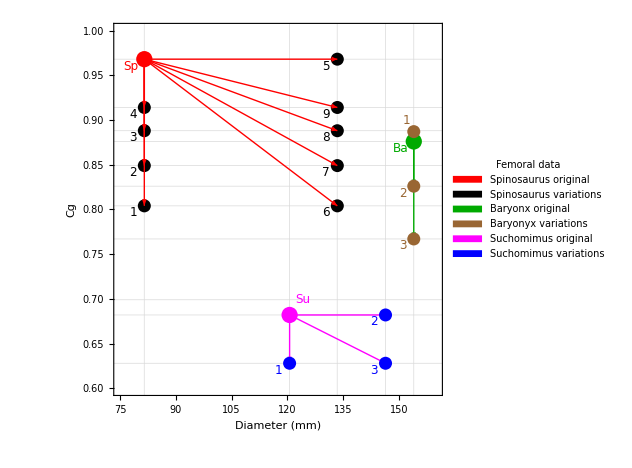

```mathematica
sensitivityvarplotfemur = Graphics[{{Red,PointSize[.025],Point[spinorawv[[1]]]},{Black,PointSize[.02],Map[Point,Drop[Drop[spinorawv,-2],1]]},
{Red, Arrowheads[0.03],Table[Arrow[{spinorawv[[1]],spinorawv[[k]]}],{k,2,10}]},

Table[Text[Style[ToString[i-1],12,Italic],spinorawv[[i]]+{-2,-.015},{1,-1}],{i,2,10}],
Text[Style["Sp",12,Italic,Red],spinorawv[[1]]+{-1.5,-.015},{1,-1}],


{Darker[Green],PointSize[.025],Point[baryrawv[[1]]]},
{Darker[Green], Arrowheads[0.03],Table[Arrow[{baryrawv[[1]],baryrawv[[k]]}],{k,2,4}]},
{Brown,PointSize[.02],Map[Point,Drop[baryrawv,1]]},
Text[Style[ToString[1],12,Italic,Brown],baryrawv[[2]]+{-1,.005},{1,-1}],
Table[Text[Style[ToString[i-1],12,Italic,Brown],baryrawv[[i]]+{-2,-.015},{1,-1}],{i,3,4}],
Text[Style["Ba",12,Italic,Darker[Green]],baryrawv[[1]]+{-1.5,-.015},{1,-1}],


{Magenta,PointSize[.025],Point[suchorawv[[1]]]},
{Magenta, Arrowheads[0.03],Table[Arrow[{suchorawv[[1]],suchorawv[[k]]}],{k,2,Length[suchorawv]}]},
{Blue,PointSize[.02],Map[Point,Drop[suchorawv,1]]},
Text[Style[ToString[1],12,Italic,Blue],suchorawv[[2]]+{-2,-.015},{1,-1}],
Table[Text[Style[ToString[i-1],12,Italic,Blue],suchorawv[[i]]+{-2,-.015},{1,-1}],{i,3,4}],
Text[Style["Su",12,Italic,Magenta],suchorawv[[1]]+{1.5,.01},{-1,-1},Background->White],
Inset[swl4, Scaled[{0.03,0.25}],{Left,Center},Background->White]
},
PlotRange->{{75,160},{0.6,1}},
Frame-> True,FrameStyle-> Directive[12,Black],
FrameLabel->{"Diameter (mm)","Cg"},
FrameTicks-> {{Automatic,DeleteCases[Join[spinovcgs,suchovcgs,baryvcgs],a_/;a==0.887 || a == 0.689]},{Automatic,Join[spinovds,suchovds,baryvds]}},
GridLines-> {Join[spinovds,suchovds,baryvds],DeleteCases[Join[spinovcgs,suchovcgs,baryvcgs],a_/;a==0.887 || a == 0.689]},
AspectRatio->1, ImageSize->mswordsize
]
```

```mathematica
Export["figureS4plot.tif",Rasterize[sensitivityvarplotfemur,ImageResolution->300],"TIFF"]
```

figureS4plot.tif

## Process Raw pFDA Data

```mathematica
Clear[combinewds,expandwd,makecfthres,safemean,classifytaxa]
```

```mathematica
makewd[replist_]:= 
Module[{repclean,repg},
repclean = DeleteCases[replist,{}|{""}|""];
repg =  DeleteCases[GatherBy[repclean,Last],{}|{""}];
WeightedData[#[[2]],#[[1]]]&[Transpose[Map[{Total[#[[All,1]]],#[[1,2]]}&,repg]]]
];
```

```mathematica
expandwd[wd_]:= 
Module[{min,counts},
min = Min[wd[[2,2]]];
counts = Map[Round[#*min]&,wd[[2,2]]];
Flatten[MapThread[Table[#1,{#2}]&,{wd[[2,1]],counts}]]
];
```

```mathematica
combinewds[wds_List]:= 
Module[{wdslist,wdslg},
wdslist = Flatten[Map[Transpose,wds[[All,2]]],1];
wdslg =Transpose[Map[{#[[1,1]],Total[#[[All,2]]]}&,GatherBy[wdslist,First]]];
WeightedData[wdslg[[1]],wdslg[[2]]]
];
```

```mathematica
combinewds[{wd_WeightedData}]:= wd;
```

```mathematica
combinewds[wd_WeightedData]:= wd;
```

```mathematica
makecfthres[diverv_,nondiverv_,thr_]:=
Module[{diverties,nondiverties},
{{Count[diverv,a_/;a> thr],Count[diverv,a_/;a< thr]},
{Count[nondiverv,a_/;a> thr],Count[nondiverv,a_/;a< thr]}}//N
];
```

```mathematica
safemean[thing_]:= If[Length[thing]==0,thing,Mean[thing]];
```

```mathematica
classifytaxa[taxawdlist_,pthres_]:=
Module[{p2s,names,f0d0p2s,f0d2p2s},
p2s = Map[safemean[Flatten[#]]&,(taxawdlist[[All,2]]/.a_WeightedData:> Mean[a])];
names = taxawdlist[[All,1]];
f0d0p2s = Pick[p2s,names/.nondivingpickrules ,1];
f0d2p2s =  Pick[p2s,names/.divingpickrules,1];
makecfthres[f0d2p2s,f0d0p2s,pthres]
];
```

```mathematica
Clear[datasetname,dirname,rawscf,rawsp,rawloocvcf,rawloocvp,rawbootcf,rawbootp,rpb2,
spinovariants, spwdlist,spspinowdlist,sptrainingwdlist,loocvpwdlist,sacc,sbal,smcc,loocvacc,loocvbal,loocvmcc,bootaccwd,bootbalwd,bootmccwd,loocvpspinowdlist,
bootpspinowdlist,loocvptrainingwdlist,bootptrainingwdlist,bootpwdlist,loocvcfs,loocvaccwd,loocvbalwd,loocvmccwd]
```

```mathematica
processdatasetrun::flist="The file `filename` is not present";
```

```mathematica
processdatasetrun[filelist_]:=
Module[{datasetname,dirname,rawscf,rawsp,rawloocvcf,rawloocvp,,rawbootcf,rawbootp,rpb2,bootpwd,
spinovariants, spwdlist,spspinowdlist,sptrainingwdlist,loocvpwdlist,loocvps,sacc,sbal,smcc,loocvacc,loocvbal,loocvmcc,bootaccwd,bootbalwd,bootmccwd,loocvpspinowdlist,
bootpspinowdlist,loocvptrainingwdlist,bootptrainingwdlist,bootpwdlist,loocvcfs,rawbootcf1,loocvaccwd,loocvbalwd,loocvmccwd,fnamelist,expectednames,present,npos,rawloocvp1,rawbootp1},
datasetname =StringSplit[FileNameSplit[ filelist[[1]]][[2]],"_"][[1]];
dirname = DirectoryName[filelist[[1]]];
rawscf = ToExpression[ToString[ Import[StringJoin[dirname,"singlepredictionconfusionmatrices.csv"]]]];
rawsp =   Map[{#[[1]],ToExpression[ToString[Drop[#,1]]]}&, Import[StringJoin[dirname,"singlepredictionprobabilites.csv"]]];

rawloocvcf =  ToExpression[ToString[ Import[StringJoin[dirname,"loocvpredictionconfusionmatrices.csv"]]]];
rawloocvp =rawloocvp1 =  Map[{#[[1]],ToExpression[ToString[Drop[#,1]]]}&,Import[StringJoin[dirname,"loocvpredictionprobabilites.csv"]]];

rawbootcf =Map[ToExpression[ToString[ #]]&,  Import[StringJoin[dirname,"bspredictionconfusionmatrices.csv"]]];
rawbootp1 =   Map[{#[[1]],ToExpression[ToString[Drop[#,1]]]}&,Import[StringJoin[dirname,"bspredictionprobabilites.csv"]]]/.{Int64->1,Tuple->1,Real->1};
rawbootp = DeleteCases[Map[{#[[1]],(#[[2,1]]/.{_,-1.}->"")/.{"",a_List}->{a}}&,rawbootp1],{_String,{""}}];

spinovariants = rawsp[[All,1]];

spwdlist = SortBy[Map[{#[[1]],makewd[Flatten[#[[2]],1]]}&,rawsp],First];
spspinowdlist = Cases[spwdlist,{name_,_}/;MemberQ[spinovariants,name]];
sptrainingwdlist = DeleteCases[spwdlist,{name_,_}/;MemberQ[spinovariants,name]];

loocvpwdlist = SortBy[Map[{#[[1,1]],Map[makewd[#]&,Flatten[#[[All,2]],1]]}&,GatherBy[rawloocvp,First]],First];
loocvpspinowdlist = Cases[loocvpwdlist,{name_,_}/;MemberQ[spinovariants,name]];
loocvptrainingwdlist = DeleteCases[loocvpwdlist,{name_,_}/;MemberQ[spinovariants,name]];

rpb2 =SortBy[Map[{#[[1,1]],Flatten[#[[All,2]],1]}&,GatherBy[rawbootp,First]],First];
bootpwdlist =  Map[{#[[1]],makewd[#[[2]]]}&,rpb2];
bootpspinowdlist = Cases[bootpwdlist,{name_,_}/;MemberQ[spinovariants,name]];
bootptrainingwdlist = DeleteCases[bootpwdlist,{name_,_}/;MemberQ[spinovariants,name]];

sacc=Mean[makewd[Flatten[rawscf,2]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> accuracy[{{a,c},{b,d}}]//N]];
sbal =Mean[makewd[Flatten[rawscf,2]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> balanced[{{a,c},{b,d}}]//N]];
smcc =Mean[makewd[Flatten[rawscf,2]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> matthews[{{a,c},{b,d}}]//N]];

loocvcfs = classifytaxa[loocvptrainingwdlist,0.5];
loocvacc = accuracy[Transpose[loocvcfs]];
loocvbal = balanced[Transpose[loocvcfs]];
loocvmcc = matthews[Transpose[loocvcfs]];

loocvaccwd =Map[makewd,Flatten[rawloocvcf,1]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> accuracy[{{a,c},{b,d}}]//N];
loocvbalwd =Map[makewd,Flatten[rawloocvcf,1]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> balanced[{{a,c},{b,d}}]//N];
loocvmccwd =Map[makewd,Flatten[rawloocvcf,1]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> matthews[{{a,c},{b,d}}]//N];

bootaccwd =Map[makewd,Flatten[rawbootcf,1]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> accuracy[{{a,c},{b,d}}]//N];
bootbalwd =Map[makewd,Flatten[rawbootcf,1]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> balanced[{{a,c},{b,d}}]//N];
bootmccwd =Map[makewd,Flatten[rawbootcf,1]/.{a_?NumberQ,b_?NumberQ,c_?NumberQ,d_?NumberQ}:> matthews[{{a,c},{b,d}}]//N];

{datasetname,
{sacc,
sbal,
smcc,
loocvacc,
loocvbal,
loocvmcc,
"",
"",
"",
bootaccwd,
bootbalwd,
bootmccwd,
loocvaccwd,
loocvbalwd,
loocvmccwd
},
{spspinowdlist,
loocvpspinowdlist,
{},
bootpspinowdlist,
{}
},
{sptrainingwdlist,
loocvptrainingwdlist,
{},
bootptrainingwdlist,
{}
}
}
];
```

```mathematica
datalistDnew = Map[processdatasetrun,fnamesbydirDnew];
```

```mathematica
datalistFnew = Map[processdatasetrun,fnamesbydirFnew];
```

## Decision Boundary Variation

```mathematica
{femurspinoadjpts,mcentroids, pointranges ,centroids, lineparams}=Get["boundary and centroid data"];
```

```mathematica
spinonames2 = {"Su","Ba","Sp"};
```

```mathematica
xlines[pt_,armlen_]:= {Line[{pt-{armlen,0},pt+{armlen,0}}],Line[{pt-{0,armlen},pt+{0,armlen}}]};
```

```mathematica
xlines2[pt_,{armlen1_,armlen2_}]:= {Line[{pt-{armlen1,0},pt+{armlen1,0}}],Line[{pt-{0,armlen2},pt+{0,armlen2}}]};
```

```mathematica
markers = {Graphics[{Thick,Line[{{-0.5,0},{0.5,0}}]},ImageSize->100],Graphics[{Thick,xlines[{0,0},0.5]},ImageSize-> 100],Graphics[{PointSize[.33],Point[{0,0}]},ImageSize->100]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
plotranges ={pointranges[[1]],MinMax[ Flatten[{femurspinoadjpts[[All,2]], Table[{{lineparams[[i]].{pointranges[[1,1]],1},lineparams[[i]].{pointranges[[1,2]],1}}},{i,Length[lineparams]}]}]]}
```

{{-0.602994,2.24931},{0.172354,0.72605}}

```mathematica
scales =Map[#[[2]]-#[[1]]&,plotranges]
```

{2.8523,0.553696}

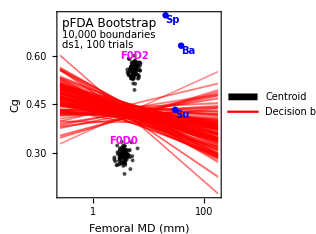

```mathematica
pfdadeclines = Graphics[{Table[{Red,Opacity[0.2],Thin,Line[{{pointranges[[1,1]],lineparams[[i]].{pointranges[[1,1]],1}},{pointranges[[1,2]],lineparams[[i]].{pointranges[[1,2]],1}}}]},{i,Length[lineparams]}],
{Black,Opacity[0.7],PointSize[.012],Map[Point,Flatten[centroids,1]]},
{Thick,Magenta,xlines2[mcentroids[[1]],0.02*scales],xlines2[mcentroids[[2]],0.02*scales]}},
FrameStyle-> Directive[10,Black,"Arial"],FrameLabel-> {"Femoral MD (mm)","Cg"},
PlotRange-> plotranges,PlotRangePadding->Scaled[0.03],PlotRangeClipping->True, AspectRatio-> 1,Frame-> True,FrameTicks-> {{Automatic,None},{log10ticks,topticklabel[#1,#2,"A"]&}},
Epilog->{Text[Style["pFDA Bootstrap",12,Black],Scaled[{0.03,0.97}],{-1,1}],
Text[Style["10,000 boundaries",10,Black],Scaled[{0.03,0.90}],{-1,1}],Text[Style["ds1, 100 trials",10,Black],Scaled[{0.03,0.85}],{-1,1}],
Text[Style["F0D2",10,Magenta,Italic,Bold,"Arial"],mcentroids[[2]]+{0,0.045},{0,-1}],
Text[Style["F0D0",10,Magenta,Italic,Bold,"Arial"],mcentroids[[1]]+{0,0.045},{0,-1}],
Inset[swl1,Scaled[{0.02,0.02}],{Left,Bottom}],
Table[{Blue,PointSize[.02],Point[femurspinoadjpts[[k]]]},{k,1,Length[spinonames2]}],
Table[Text[Style[spinonames2[[k]],Blue,10,Italic,Bold],femurspinoadjpts[[k]],{-1,1}],{k,1,Length[spinonames2]}]
}, ImageSize-> mswordsize/2]
```

## BCa Bootstrap CI from pFDA output

DiCiccio TJ, Efron B (1996) Bootstrap Confidence Intervals . Statistical Science 11 : 189 - 228.
Efron B, Tibshirai RJ (1994) An introduction to the bootstrap. Chapman & Hall/CRC: Boca Raton; p 186.
Efron, Bradley, and Balasubramanian Narasimhan. “The automatic construction of bootstrap confidence intervals.” Journal of Computational and Graphical Statistics 29.3 (2020): 608-619.

```mathematica
expandwd[wd_WeightedData]:= Flatten[MapThread[Table[#1,{#2}]&,{wd[[2,1]],Round[wd[[2,2]]]}]];
```

```mathematica
bcaadjust[singlewd_,jackwds_,bootwds_,alpha_]:=
Module[{jmean,jdiff,ahat,values,valuesx,qs,ntrials,single,z0hat,zalphahat,low,hi,pros,ciqs},
jmean = Mean[combinewds[jackwds]];
jdiff = jmean-Map[Mean,jackwds];
If[MinMax[jdiff]=={0.,0.},
ahat = 0;
,
ahat = (1/6)Total[jdiff^3]/(Total[jdiff^2]^(3/2));
];

values = combinewds[bootwds];
qs = Quantile[values,{0.5,0.025,0.975}];
valuesx = expandwd[values];
ntrials = Length[valuesx];
single = singlewd;
z0hat = InverseCDF[NormalDistribution[0,1],(Count[valuesx,a_/;a<single]+ 0.5*Count[values,a_/;a == single])/ntrials];

zalphahat = InverseCDF[NormalDistribution[0,1],alpha/2];
low = z0hat+ (z0hat+ zalphahat)/(1-ahat(z0hat+ zalphahat));
hi=  z0hat+ (z0hat - zalphahat )/(1-ahat(z0hat-zalphahat));
pros = Map[CDF[NormalDistribution[0,1],#]&,{low,hi}];
ciqs = InverseCDF[EmpiricalDistribution[values],pros];
{{single,ciqs[[1]],ciqs[[2]]}}
];
```

```mathematica
prand[a_]:= 2(1-a);
```

```mathematica
trainingsetcis[ds_]:=
Map[Flatten,{{ds[[1]],"Accuracy",bcaadjust[ds[[2,1]],ds[[2,13]],ds[[2,10]],0.05]},
{ds[[1]],"Prand",Map[prand,bcaadjust[ds[[2,1]],ds[[2,13]],ds[[2,10]],0.05]]},
{ds[[1]],"Balanced accuracy",bcaadjust[ds[[2,2]],ds[[2,14]],ds[[2,11]],0.05]},
{ds[[1]],"Matthews",bcaadjust[ds[[2,3]],ds[[2,15]],ds[[2,12]],0.05]}}];
```

```mathematica
Clear[names,singles,jackwds,bootwds,cis]
```

```mathematica
spinopredictioncis[ds_]:=
Module[{names,singles,jackwds,bootwds,cis},
names = ds[[3,4,All,1]];
singles = Map[Mean,ds[[3,1,All,2]]];
jackwds = ds[[3,2,All,2]];
bootwds = ds[[3,4,All,2]];
cis = MapThread[{ds[[1]],#1,bcaadjust[#2,#3,#4,0.05]}&,{names,singles,jackwds,bootwds}];
Map[Flatten,cis]
];
```

```mathematica
bootheader = {{"Dataset","Metric","Median","95% CI low","95% CI hi"}};
```

```mathematica
datasetexp1 = {"original","no g,p","fix errors","fix & remove small"};
fullexp = Flatten[Map[{{#,"Femur"},{#,"Rib"}}&,datasetexp1],1];
Dexprules = Table[StringJoin["D",ToString[i]]-> StringJoin[fullexp[[i,1]]," ",fullexp[[i,2]]],{i,1,8}];
Fexprules = Table[StringJoin["F",ToString[i]]-> StringJoin[fullexp[[i,1]]," ",fullexp[[i,2]]],{i,1,8}]
```

{F1→original Femur,F2→original Rib,F3→no g,p Femur,F4→no g,p Rib,F5→fix errors Femur,F6→fix errors Rib,F7→fix & remove small Femur,F8→fix & remove small Rib}

### Training Data - Table 7

```mathematica
Dtrainingci = Map[trainingsetcis,datalistDnew];
```

```mathematica
Ftrainingcis =  Map[trainingsetcis,datalistFnew];
```

```mathematica
Join[bootheader,Map[{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&,Map[Flatten,Flatten[Dtrainingci,1]/.cvnamerules]]]/. num_?NumberQ:> NumberForm[num,{4,3}]//TableForm
```

Dataset | Metric | Median | 95% CI low | 95% CI hi
D1 | Accuracy | 0.795 | 0.718 | 0.863
D1 | Prand | 0.410 | 0.564 | 0.274
D1 | Balanced accuracy | 0.794 | 0.717 | 0.863
D1 | Matthews | 0.607 | 0.470 | 0.752
D2 | Accuracy | 0.821 | 0.696 | 0.884
D2 | Prand | 0.357 | 0.607 | 0.232
D2 | Balanced accuracy | 0.819 | 0.706 | 0.883
D2 | Matthews | 0.637 | 0.415 | 0.767
D3 | Accuracy | 0.833 | 0.725 | 0.892
D3 | Prand | 0.333 | 0.549 | 0.216
D3 | Balanced accuracy | 0.833 | 0.725 | 0.892
D3 | Matthews | 0.673 | 0.464 | 0.792
D4 | Accuracy | 0.891 | 0.739 | 0.946
D4 | Prand | 0.217 | 0.522 | 0.109
D4 | Balanced accuracy | 0.877 | 0.749 | 0.939
D4 | Matthews | 0.765 | 0.467 | 0.883

```mathematica
Join[bootheader,Map[{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]]}&,Map[Flatten,Flatten[Ftrainingcis,1]/.cvnamerules]]]/. num_?NumberQ:> NumberForm[num,{4,3}]//TableForm
```

Dataset | Metric | Median | 95% CI low | 95% CI hi
F1 | Accuracy | 0.836 | 0.771 | 0.894
F1 | Prand | 0.327 | 0.458 | 0.212
F1 | Balanced accuracy | 0.841 | 0.781 | 0.899
F1 | Matthews | 0.655 | 0.528 | 0.770
F2 | Accuracy | 0.772 | 0.648 | 0.846
F2 | Prand | 0.457 | 0.704 | 0.309
F2 | Balanced accuracy | 0.778 | 0.677 | 0.849
F2 | Matthews | 0.521 | 0.332 | 0.670
F3 | Accuracy | 0.895 | 0.839 | 0.950
F3 | Prand | 0.211 | 0.323 | 0.099
F3 | Balanced accuracy | 0.897 | 0.840 | 0.945
F3 | Matthews | 0.769 | 0.652 | 0.874
F4 | Accuracy | 0.882 | 0.772 | 0.941
F4 | Prand | 0.235 | 0.456 | 0.118
F4 | Balanced accuracy | 0.863 | 0.740 | 0.922
F4 | Matthews | 0.700 | 0.472 | 0.841

### Spinosaurid predictions

```mathematica
Flatten[GatherBy[Cases[rawsenspts,{_,"Femur",__}],First],1]//TableForm
```

Spinosaurus | Femur | 81.52 | 1.91126 | 0.968 | Fabbri | Fabbri
Spinosaurus | Femur | 81.52 | 1.91126 | 0.804 | Fabbri | Low of 3 CT scans
Spinosaurus | Femur | 81.52 | 1.91126 | 0.849 | Fabbri | Medium of 3 CT scans
Spinosaurus | Femur | 81.52 | 1.91126 | 0.888 | Fabbri | High of 3 CT scans
Spinosaurus | Femur | 81.52 | 1.91126 | 0.914 | Fabbri | Fabbri et al claim in reply
Spinosaurus | Femur | 133.434 | 2.12527 | 0.968 | scaled to adult | Fabbri
Spinosaurus | Femur | 133.434 | 2.12527 | 0.804 | scaled to adult | Low of 3 CT scans
Spinosaurus | Femur | 133.434 | 2.12527 | 0.849 | scaled to adult | Medium of 3 CT scans
Spinosaurus | Femur | 133.434 | 2.12527 | 0.888 | scaled to adult | High of 3 CT scans
Spinosaurus | Femur | 133.434 | 2.12527 | 0.914 | scaled to adult | Fabbri et al claim in reply
Spinosaurus | Femur | 57.39 | 1.75884 | 0.699 | Baby femur | SB scan high
Spinosaurus | Femur | 57.39 | 1.75884 | 0.689 | Baby femur | SB scan low
Suchomimus | Femur | 120.6 | 2.08135 | 0.682 | Fabbri | Fabbri
Suchomimus | Femur | 120.6 | 2.08135 | 0.628 | Fabbri | From SB scan
Suchomimus | Femur | 146.4 | 2.16554 | 0.682 | Actual max GAD500 | Fabbri
Suchomimus | Femur | 146.4 | 2.16554 | 0.628 | Actual min GAD500 | From SB scan
Baryonyx | Femur | 154 | 2.18752 | 0.876 | Fabbri | Fabbri
Baryonyx | Femur | 154 | 2.18752 | 0.887 | Fabbri | Scanned Cg high
Baryonyx | Femur | 154 | 2.18752 | 0.826 | Fabbri | Scanned Cg median
Baryonyx | Femur | 154 | 2.18752 | 0.767 | Fabbri | Scanned Cg low

```mathematica
Flatten[GatherBy[Cases[rawsenspts,{_,"Rib",__}],First],1]//TableForm
```

Spinosaurus | Rib | 35.1 | 1.54531 | 0.931 | Fabbri | Fabbri
Spinosaurus | Rib | 35.1 | 1.54531 | 0.8379 | Fabbri | Scaled by 0.9
Spinosaurus | Rib | 57.4517 | 1.7593 | 0.931 | Scaled to adult | Fabbri
Spinosaurus | Rib | 57.4517 | 1.7593 | 0.8379 | scaled to adult | Scaled by 0.9
Baryonyx | Rib | 42.2 | 1.62531 | 0.921 | Fabbri | Fabbri
Baryonyx | Rib | 42.2 | 1.62531 | 0.8289 | Fabbri | Scaled by 0.9

#### Formatting and case names

```mathematica
spinofemurcasenamerules = {"Spinosaurus_"->"Spinosaurus0","Spinosaurus_.1"->"Spinosaurus1","Spinosaurus_.2"->"Spinosaurus2","Spinosaurus_.3"->"Spinosaurus3","Spinosaurus_.4"->"Spinosaurus4","Spinosaurus_.5"->"Spinosaurus5","Spinosaurus_.6"->"Spinosaurus6","Spinosaurus_.7"->"Spinosaurus7","Spinosaurus_.8"->"Spinosaurus8","Spinosaurus_.9"->"Spinosaurus9","Spinosaurus_.10"->"Spinosaurus10","Spinosaurus_.11"->"Spinosaurus11"};
```

```mathematica
spinoribcasenamerules = {"Spinosaurus"-> "Spinosaurus0","Spinosaurus.1"->"Spinosaurus1","Spinosaurus.2"->"Spinosaurus2","Spinosaurus.3"->"Spinosaurus3"}
```

{Spinosaurus→Spinosaurus0,Spinosaurus.1→Spinosaurus1,Spinosaurus.2→Spinosaurus2,Spinosaurus.3→Spinosaurus3}

```mathematica
spinolexorder = Map[ToExpression[#[[-1]]]&,GatherBy[Map[StringSplit[#,"."]&, datalistDnew[[1]][[3,4,All,1]]/.{"Baryonyx"-> "Baryonyx.0","Spinosaurus_"-> "Spinosaurus_.0","Suchomimus"->"Suchomimus.0"}],First],{2}][[2]]
```

{0,1,10,11,2,3,4,5,6,7,8,9}

```mathematica
spinogoodorder =Drop[ Ordering[spinolexorder],-2]+4
```

{5,6,9,10,11,12,13,14,15,16}

```mathematica
spinotaxagoodorder = Join[Range[4],spinogoodorder,Range[17,17+3]]
```

{1,2,3,4,5,6,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
suchofemurcasenamerules = {"Suchomimus"->"Suchomimus0","Suchomimus.1"->"Suchomimus1","Suchomimus.2"->"Suchomimus2","Suchomimus.3"->"Suchomimus3"};
```

```mathematica
baryonyxfemurcasenamerules = {"Baryonyx"->"Baryonyx0","Baryonyx.1"->"Baryonyx1","Baryonyx.2"->"Baryonyx2","Baryonyx.3"->"Baryonyx3"};
```

```mathematica
casenamerules = Join[spinofemurcasenamerules,spinoribcasenamerules,baryonyxfemurcasenamerules,suchofemurcasenamerules];
```

```mathematica
casenamerules[[1]]
```

Spinosaurus_→Spinosaurus0

#### Calculation

```mathematica
spppd1 = spinopredictioncis[datalistDnew[[1]]]/.casenamerules
```

{{D1,Baryonyx0,0.94,0.83,0.99},{D1,Baryonyx1,0.95,0.85,0.99},{D1,Baryonyx2,0.8878,0.76,0.98},{D1,Baryonyx3,0.7698,0.59,0.93},{D1,Spinosaurus0,0.9709,0.93,1.},{D1,Spinosaurus1,0.8092,0.69,0.94},{D1,Spinosaurus10,0.4924,0.39,0.67},{D1,Spinosaurus11,0.459,0.34,0.61},{D1,Spinosaurus2,0.8857,0.79,0.97},{D1,Spinosaurus3,0.9281,0.84,0.99},{D1,Spinosaurus4,0.9489,0.87,0.99},{D1,Spinosaurus5,0.9799,0.92,1.},{D1,Spinosaurus6,0.8264,0.69,0.96},{D1,Spinosaurus7,0.896,0.78,0.98},{D1,Spinosaurus8,0.9352,0.85,0.99},{D1,Spinosaurus9,0.9524,0.88,1.},{D1,Suchomimus0,0.4884,0.31,0.71},{D1,Suchomimus1,0.3136,0.15,0.51},{D1,Suchomimus2,0.4997,0.3,0.73},{D1,Suchomimus3,0.3236,0.15,0.53}}

```mathematica
spppd2 = spinopredictioncis[datalistDnew[[2]]]/.casenamerules
```

{{D2,Baryonyx0,1.,0.97,1.},{D2,Baryonyx1,0.97,0.86,1.},{D2,Spinosaurus0,0.9914,0.97,1.},{D2,Spinosaurus1,0.9691,0.89,1},{D2,Spinosaurus2,1.,0.97,1.},{D2,Spinosaurus3,0.9794,0.9,1.}}

```mathematica
spppf1 = spinopredictioncis[datalistFnew[[1]]]/.casenamerules
```

{{F1,Baryonyx0,0.97,0.9,1.},{F1,Baryonyx1,0.98,0.92,1.},{F1,Baryonyx2,0.9114,0.82,1.},{F1,Baryonyx3,0.7118,0.57,0.95},{F1,Spinosaurus0,0.999,0.97,1.},{F1,Spinosaurus1,0.8462,0.74,1.},{F1,Spinosaurus10,0.3658,0.23,0.53},{F1,Spinosaurus11,0.3144,0.16,0.46},{F1,Spinosaurus2,0.9373,0.85,1.},{F1,Spinosaurus3,0.9729,0.93,1.},{F1,Spinosaurus4,0.9856,0.95,1.},{F1,Spinosaurus5,0.9946,0.98,1.},{F1,Spinosaurus6,0.8304,0.72,1.},{F1,Spinosaurus7,0.9298,0.83,1.},{F1,Spinosaurus8,0.9699,0.9,1.},{F1,Spinosaurus9,0.9801,0.95,1.},{F1,Suchomimus0,0.2539,0.04,0.41},{F1,Suchomimus1,0.0898,0.,0.19},{F1,Suchomimus2,0.245,0.03,0.42},{F1,Suchomimus3,0.0855,0.,0.2}}

```mathematica
spppf2 = spinopredictioncis[datalistFnew[[2]]]/.casenamerules
```

{{F2,Baryonyx0,0.9702,0.93,1.},{F2,Baryonyx1,0.8915,0.79,0.98},{F2,Spinosaurus0,0.97,0.91,1.},{F2,Spinosaurus1,0.8804,0.79,0.98},{F2,Spinosaurus2,0.97,0.89,1.},{F2,Spinosaurus3,0.8978,0.78,0.98}}

```mathematica
spff2= spinopredictioncis[datalistFnew[[2]]]/.casenamerules
```

{{F2,Baryonyx0,0.9702,0.93,1.},{F2,Baryonyx1,0.8915,0.79,0.98},{F2,Spinosaurus0,0.97,0.91,1.},{F2,Spinosaurus1,0.8804,0.79,0.98},{F2,Spinosaurus2,0.97,0.89,1.},{F2,Spinosaurus3,0.8978,0.78,0.98}}

### Table 9

```mathematica
Join[Map[Flatten,Transpose[{spppd1[[spinotaxagoodorder]],Map[Drop[#,2]&,spppf1[[spinotaxagoodorder]]]}]],
Map[Flatten,Transpose[{spppd2,Map[Drop[#,2]&,spppf2]}]]]/.x_?NumberQ:>NumberForm[x//N,{3,2}]//TableForm
```

D1 | Baryonyx0 | 0.94 | 0.83 | 0.99 | 0.97 | 0.90 | 1.00
D1 | Baryonyx1 | 0.95 | 0.85 | 0.99 | 0.98 | 0.92 | 1.00
D1 | Baryonyx2 | 0.89 | 0.76 | 0.98 | 0.91 | 0.82 | 1.00
D1 | Baryonyx3 | 0.77 | 0.59 | 0.93 | 0.71 | 0.57 | 0.95
D1 | Spinosaurus0 | 0.97 | 0.93 | 1.00 | 1.00 | 0.97 | 1.00
D1 | Spinosaurus1 | 0.81 | 0.69 | 0.94 | 0.85 | 0.74 | 1.00
D1 | Spinosaurus2 | 0.89 | 0.79 | 0.97 | 0.94 | 0.85 | 1.00
D1 | Spinosaurus3 | 0.93 | 0.84 | 0.99 | 0.97 | 0.93 | 1.00
D1 | Spinosaurus4 | 0.95 | 0.87 | 0.99 | 0.99 | 0.95 | 1.00
D1 | Spinosaurus5 | 0.98 | 0.92 | 1.00 | 0.99 | 0.98 | 1.00
D1 | Spinosaurus6 | 0.83 | 0.69 | 0.96 | 0.83 | 0.72 | 1.00
D1 | Spinosaurus7 | 0.90 | 0.78 | 0.98 | 0.93 | 0.83 | 1.00
D1 | Spinosaurus8 | 0.94 | 0.85 | 0.99 | 0.97 | 0.90 | 1.00
D1 | Spinosaurus9 | 0.95 | 0.88 | 1.00 | 0.98 | 0.95 | 1.00
D1 | Suchomimus0 | 0.49 | 0.31 | 0.71 | 0.25 | 0.04 | 0.41
D1 | Suchomimus1 | 0.31 | 0.15 | 0.51 | 0.09 | 0.00 | 0.19
D1 | Suchomimus2 | 0.50 | 0.30 | 0.73 | 0.25 | 0.03 | 0.42
D1 | Suchomimus3 | 0.32 | 0.15 | 0.53 | 0.09 | 0.00 | 0.20
D2 | Baryonyx0 | 1.00 | 0.97 | 1.00 | 0.97 | 0.93 | 1.00
D2 | Baryonyx1 | 0.97 | 0.86 | 1.00 | 0.89 | 0.79 | 0.98
D2 | Spinosaurus0 | 0.99 | 0.97 | 1.00 | 0.97 | 0.91 | 1.00
D2 | Spinosaurus1 | 0.97 | 0.89 | 1.00 | 0.88 | 0.79 | 0.98
D2 | Spinosaurus2 | 1.00 | 0.97 | 1.00 | 0.97 | 0.89 | 1.00
D2 | Spinosaurus3 | 0.98 | 0.90 | 1.00 | 0.90 | 0.78 | 0.98

## Bootstrap Histograms

```mathematica
weighteddatahistoline[wdslist_]:=
Module[{wd,tlst,spts,pairs,sum,adjpts},
wd = combinewds[wdslist];
tlst = Transpose[wd[[2]]];
spts = SortBy[tlst,First];
pairs = Partition[spts,2,1];
sum = Total[Map[(#[[2,1]]-#[[1,1]])#[[1,2]]&,pairs]];
Map[{#[[1]],#[[2]]/sum}&,spts]
];
```

```mathematica
plothisto2[bootlist_,metricname_,plotname_,color_]:=
Module[{datawd,mm,hline,qs},
datawd =combinewds[bootlist];
qs = Quantile[datawd,{0.025,0.5,0.975}];
hline = weighteddatahistoline[bootlist];
mm = Map[MinMax,Transpose[hline]];
ListPlot[hline,Joined->True,InterpolationOrder->0,Filling-> Axis,
PlotRange->mm,PlotRangePadding-> {{Scaled[0.05],Scaled[0.05]},{None,Scaled[0.03]}},
PlotStyle->color,
Frame-> True,FrameStyle-> Directive[10,Black],
FrameLabel->{metricname,"Probability density"},
FrameTicks-> {{Automatic,Automatic},{Automatic,Map[{#,NumberForm[#,{3,3}]}&,qs]}},
AspectRatio->1,GridLines->{qs,None},
Epilog->{Text[Style[plotname[[1]],12],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style[plotname[[2]],10],Scaled[{0.03,0.90}],{-1,1},Background->White],
Text[Style["2000 trials",10],Scaled[{0.03,0.83}],{-1,1},Background->White]
},ImageSize->mswordsize/2]
];
```

```mathematica
plothisto3[bootlist_,metricname_,plotname_,color_,bcaci_]:=
Module[{datawd,mm,hdf,qs,qs2,hline},
datawd =combinewds[bootlist];
qs = bcaci;
qs2 = Quantile[datawd,{0.025,0.5,0.975}];
hline = weighteddatahistoline[bootlist];
mm = Map[MinMax,Transpose[hline]];

ListPlot[hline,Joined->True,InterpolationOrder->0,Filling-> Axis,
PlotRange->mm,PlotRangePadding-> {{Scaled[0.05],Scaled[0.05]},{None,Scaled[0.03]}},
PlotStyle->color,
Frame-> True,FrameStyle-> Directive[10,Black],
FrameLabel->{metricname,"Probability density"},
FrameTicks-> {{Automatic,Automatic},{Automatic,Map[{#,NumberForm[#,{3,3}]}&,qs]}},
AspectRatio->1,GridLines->{Join[qs,Map[{#,Directive[Red]}&,qs2]],None},
Epilog->{Text[Style[plotname[[1]],12],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style[plotname[[2]],10],Scaled[{0.03,0.90}],{-1,1},Background->White],
Text[Style["2000 trials",10],Scaled[{0.03,0.83}],{-1,1},Background->White]
},ImageSize->mswordsize/2]
];
```

```mathematica
plothistoqs[bootlist_,metricname_,plotname_,color_,qs_,lab_]:=
Module[{hline,mm},
hline = weighteddatahistoline[bootlist];
mm = Map[MinMax,Transpose[hline]];
ListPlot[hline,Joined->True,InterpolationOrder->0,Filling-> Axis,
PlotRange->mm,PlotRangePadding-> {{Scaled[0.05],Scaled[0.05]},{None,Scaled[0.03]}},
PlotStyle->color,
Frame-> True,FrameStyle-> Directive[10,Black],
FrameLabel->{metricname,"Probability density"},
FrameTicks-> {{Automatic,Automatic},{Automatic,Join[{{mm[[1,1]]-0.007,Style[lab,12,Bold],0}},Map[{#,NumberForm[#,{3,3}]}&,qs]]}},
AspectRatio->1,GridLines->{qs,None},
Epilog->{Text[Style[plotname[[1]],12],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style[plotname[[2]],10],Scaled[{0.03,0.90}],{-1,1},Background->White],
Text[Style[plotname[[3]],10],Scaled[{0.03,0.83}],{-1,1},Background->White],
Text[Style["2000 trials",10],Scaled[{0.03,0.83-0.07}],{-1,1},Background->White]
},ImageSize->mswordsize/2]
];
```

### Training set accuracy

```mathematica
Dtrainingci[[1,1,{3,4,5}]]
```

{0.794872,0.717949,0.863248}

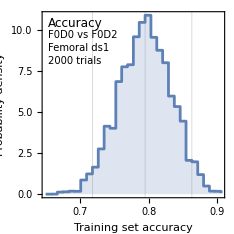

```mathematica
trainingacchisto1 = plothistoqs[datalistDnew[[1,2,10]],"Training set accuracy",{"Accuracy","F0D0 vs F0D2","Femoral ds1"},ColorData[97][1],Dtrainingci[[1,1,{3,4,5}]],"B"]
```

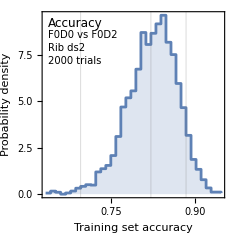

```mathematica
trainingacchisto2 = plothistoqs[datalistDnew[[2,2,10]],"Training set accuracy",{"Accuracy","F0D0 vs F0D2","Rib ds2"},ColorData[97][1],Dtrainingci[[2,1,{3,4,5}]],"D"]
```

### Spinosaurid prediction - femur dataset 1

```mathematica
baryhline = weighteddatahistoline[datalistDnew[[1]][[3,4,1,2]]];
spinohline = weighteddatahistoline[datalistDnew[[1]][[3,4,5,2]]];
suchohline = weighteddatahistoline[datalistDnew[[1]][[3,4,17,2]]];
```

```mathematica
mmsh = Map[MinMax,Transpose[Flatten[{baryhline,spinohline,suchohline},1]]]
```

{{0.11,1.},{0.000517941,20.0552}}

```mathematica
sw5 = SwatchLegend[Table[Directive[Opacity[0.7],ColorData[112][i]],{i,1,3}],{"Baryonyx","Spinosaurus","Suchomimus"},LegendMargins->0,LabelStyle->Directive[10,Black]]
```

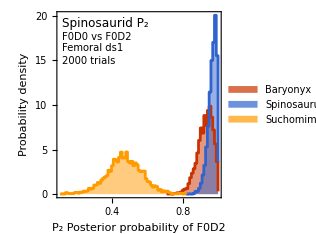

```mathematica
spinohistoplot = ListPlot[{baryhline,spinohline,suchohline},Joined->True,InterpolationOrder->0,
PlotRange->mmsh,PlotRangePadding-> {{None,Scaled[0.03]},{None,Scaled[0.03]}},
PlotStyle->ColorData[112],Filling-> Bottom,
FillingStyle->Directive[Opacity[0.5]],
Frame-> True,FrameStyle-> Directive[10,Black,"Arial"],
FrameLabel->{"P_2 Posterior probability of F0D2","Probability density"},
FrameTicks-> {{Automatic,Automatic},{Automatic,topticklabel[#1,#2,"C"]&}},
AspectRatio->1,GridLines->{None,None},
Epilog->{Text[Style["Spinosaurid P_2",12],Scaled[{0.03,0.97}],{-1,1},Background->White],
Text[Style["F0D0 vs F0D2",10],Scaled[{0.03,0.89}],{-1,1},Background->White],
Text[Style["Femoral ds1",10],Scaled[{0.03,0.83}],{-1,1},Background->White],
Text[Style["2000 trials",10],Scaled[{0.03,0.83-0.07}],{-1,1},Background->White],
Inset[sw5,Scaled[{0.03,0.4}],{Left,Bottom}]
},ImageSize->mswordsize/2]
```

```mathematica
0.829-0.643
```

0.186

```mathematica
0.884-0.643
```

0.241

```mathematica
bary1bins = 0.005*{1,1,1,1};
```

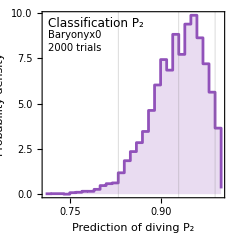
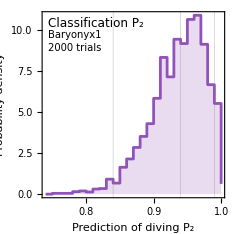
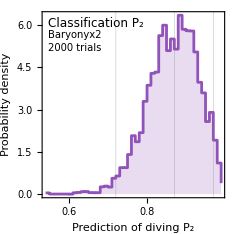
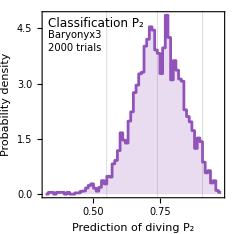

```mathematica
Table[plothisto2[datalistDnew[[1]][[3,4,i,2]],"Prediction of diving P_2",{"Classification P_2", datalistDnew[[1]][[3,4,i,1]]/.casenamerules,"Femur dataset 1"},ColorData[111][1]],{i,1,4}]
```

```mathematica
spinop2histos = Partition[Table[plothisto3[datalistDnew[[1]][[3,4,spinogoodorder[[i]],2]],"Postierior probability of diving P_2",{"Probability P_2", datalistDnew[[1]][[3,4,spinogoodorder[[i]],1]]/.casenamerules,"Femur dataset 1"},ColorData[111][1],spppd1[[spinogoodorder,{4,3,5}]][[i]]],{i,1,10}],4,4,1,{}];
```

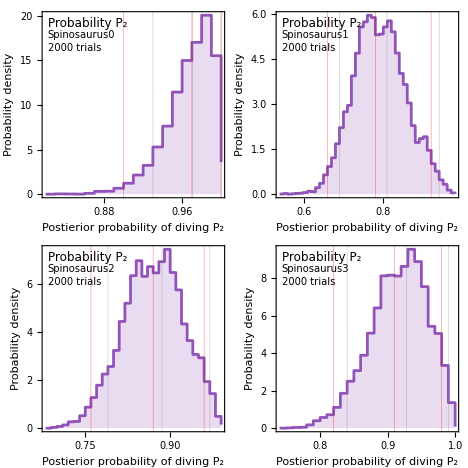
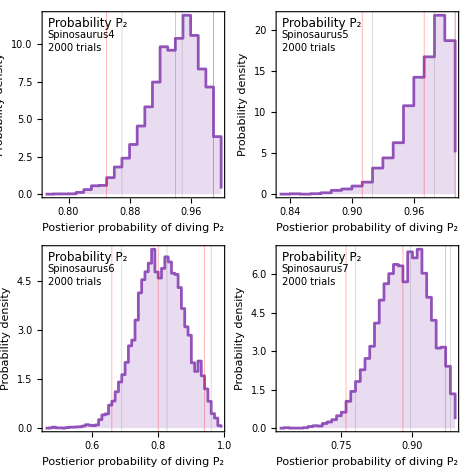
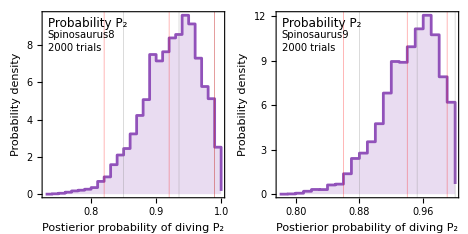

```mathematica
spinop2histofigs = Map[GraphicsGrid[If[Length[#]==4,Partition[#,2],{#}],Spacings->0,ImageSize->mswordsize]&,spinop2histos]
```

```mathematica
Table[Export[StringJoin["figureS",ToString[i+4],"plot.tif"],Rasterize[spinop2histofigs[[i]],ImageResolution->300],"TIFF"],{i,1,Length[spinop2histofigs]}]
```

{figureS5plot.tif,figureS6plot.tif,figureS7plot.tif}

### Rib 1

```mathematica
Table[plothisto2[datalistDnew[[2]][[3,4,i,2]],0.005,"Prediction of diving P_2",{"Classification P_2",datalistDnew[[2]][[3,4,i,1]]/.casenamerules,"Rib dataset 1"},ColorData[111][2]],{i,1,2}]
```

{plothisto2[WeightedData[…],0.005,Prediction of diving P_2,{Classification P_2,Baryonyx0,Rib dataset 1},RGBColor[0.969902, 0.60553, 0.0812646]],plothisto2[WeightedData[…],0.005,Prediction of diving P_2,{Classification P_2,Baryonyx1,Rib dataset 1},RGBColor[0.969902, 0.60553, 0.0812646]]}

```mathematica
Table[plothisto2[datalistDnew[[2]][[3,4,i,2]],0.005,"Prediction of diving P_2",{"Classification P_2",datalistDnew[[2]][[3,4,i,1]]/.casenamerules,"Rib dataset 1"},ColorData[111][2]],{i,3,6}]
```

{plothisto2[WeightedData[…],0.005,Prediction of diving P_2,{Classification P_2,Spinosaurus0,Rib dataset 1},RGBColor[0.969902, 0.60553, 0.0812646]],plothisto2[WeightedData[…],0.005,Prediction of diving P_2,{Classification P_2,Spinosaurus1,Rib dataset 1},RGBColor[0.969902, 0.60553, 0.0812646]],plothisto2[WeightedData[…],0.005,Prediction of diving P_2,{Classification P_2,Spinosaurus2,Rib dataset 1},RGBColor[0.969902, 0.60553, 0.0812646]],plothisto2[WeightedData[…],0.005,Prediction of diving P_2,{Classification P_2,Spinosaurus3,Rib dataset 1},RGBColor[0.969902, 0.60553, 0.0812646]]}

### Fig 13 plot

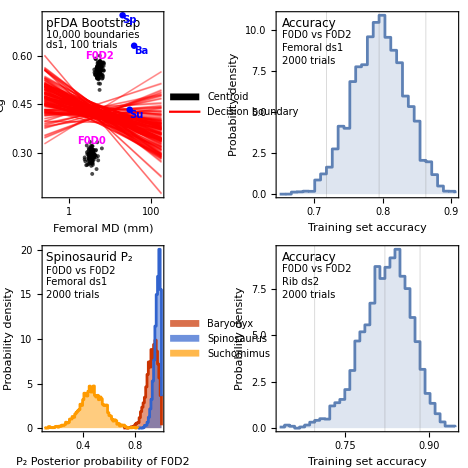

```mathematica
fig13plot = GraphicsGrid[{{pfdadeclines,trainingacchisto1},{spinohistoplot,trainingacchisto2}},Spacings->0,ImageSize-> mswordsize]
```

```mathematica
Export["figure13plot.tif",Rasterize[fig13plot,ImageResolution->300],"TIFF"]
```

figure13plot.tif